```mathematica
(*****Amin NO APPROX*****)
Clear[omegam,gammam,det,kapp2,con1,con2,sus,f,tpden,tp,delta,T2,alphare1,alphaim1,alpha1,alpha,num1,den1,omega];
{hbar,boltz,c,epsr,eps0}={1.05*10^-34,1.4*10^-23,3*10^8,1.45^2,8.854*10^-12};
{k,mass,radius,rho}={5.9*10^6,0.7365*10^-16,200*10^-9,2198};
{cavlong,waist,finesse}={1.4*10^-2,61*10^-6,100000};
afreql=k*c;
cavvol=Pi cavlong*waist^2;
sphvol=4/3 Pi radius^3;
polaris=3 sphvol*eps0*(epsr-1)/(epsr+2);
A=afreql*polaris/(2 eps0*cavvol);

{Pin,Press,scale}={11*10^-3,1*10^-2,0.01};
kapp2=Pi c/(2finesse*cavlong); (*kappa/2*)
Ein1=Sqrt[kapp2*Pin/(2 hbar* afreql)];
Pin2=Pin*scale;
Ein2=Sqrt[kapp2*Pin2/(2 hbar* afreql)];
gammam=1600*Press/(500Pi*rho*radius);

{wk0,delta}={0,-74000*2Pi};
num1=Ein1*(delta+A Cos[wk0]^2);
num2=Ein2*A Cos[wk0]^2;
den1=kapp2^2+(delta+A Cos[wk0]^2)^2;
den2=kapp2^2+(A Cos[wk0]^2)^2;
alphare1=num1/den1;
alphare2=num2/den2;
alphaim1=-Ein1*kapp2/den1;
alphaim2=-Ein2*kapp2/den2;

alpha1=Ein1^2/den1;
alpha2=Ein2^2/den2;
alpha=alpha1+alpha2+2*alphare1*alphare2+2*alphaim1*alphaim2;

{x0,Fyz}={10^-14,1};
G=A k Sin[2 k x0];
omegam=Sqrt[2 hbar A k^2 Cos[2 k x0](alpha)/mass];

{rtrap,volt,bx,Q,afreqd}={1*10^-3/Sqrt[2],600,1,1.6*10^-19,1500};
drive=Q*volt/rtrap^2;
stable=4*Q*volt/(mass*(2 Pi afreqd)^2*rtrap^2);
det[delta_]:=delta+0*A Cos[k x0]; (*effective detuning*)

Print["Pin = ",N[Pin],"   ","Press = ",N[Press],"   ","scale = ",scale,"\n","Ein1= ",Ein1,"\n","alpha = ",alpha,"\n","gammam = ",N[gammam],"\n","kapp2 = ",kapp2,"\n","detuning (effective) = ",delta/(2Pi),"   ",det,"\n","mechanical frequency (angular) = ",omegam/(2 Pi),"   ",omegam,"\n","drive = ",drive,"\n","stability parameter = ",stable]

T1=hbar*G^2*alpha^2;
(*****TRANSMISSION EXACT*****)
sus[omega_]:=(mass*(omegam^2-omega^2-I omega gammam))^-1;
f[omega_,delta_]:=T1*sus[omega]/(I*(det[delta]-omega)+kapp2);
tpden[omega_,delta_]:=-I*(det[delta]+omega)+kapp2+2det[delta] f[omega,delta];
tp[omega_,delta_]:=Norm[1-(1+I f[omega,delta])/tpden[omega,delta]*kapp2]^2;
Manipulate[{"eff det =",det[delta],Plot[tp[omega,delta],{omega,850000,870000},PlotRange->All,AxesOrigin->{850000,0}]},{{delta,-74000*2Pi},-10^3*2 Pi,-2*10^5*2Pi},{{t1,4 10^10},10^10,10^11}]
```

Pin = 0.011   Press = 0.01   scale = 0.01
Ein1= 9.9806×10^10
alpha = 5.16694×10^10
gammam = 23.1709
kapp2 = 336599.
detuning (effective) = -74000   det
mechanical frequency (angular) = 137762.   865585.
drive = 1.92×10^-10
stability parameter = 0.117394

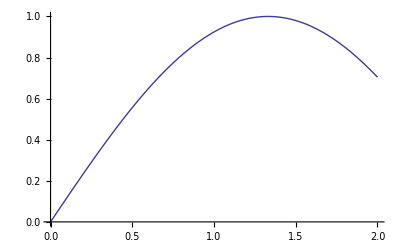

```mathematica
Plot[Sin[2 k x0],{x0,0,2 10^-7}]
```

```mathematica
0.5*Pi/k
```

2.66237×10^-7

```mathematica
waist
```

61/1000000